```mathematica
DSolve[{D[ξ[τ],τ] == λ ξ[τ],ξ[t]==Subscript[x, 0]},ξ,τ]
DSolve[{D[ξ[τ], τ]==-λ (r (f[τ]-1)^2+f[τ]-ξ[τ]),ξ[t]==Subscript[x, 0]},ξ,τ]
```

{{ξ→Function[{τ},ⅇ^(-t λ+λ τ) x_0]}}

{{ξ→Function[{τ},ⅇ^(-t λ+λ τ) (-ⅇ^(t λ) ∫_1^t ⅇ^(-λ K[1]) (-r λ-λ f[K[1]]+2 r λ f[K[1]]-r λ f[K[1]]^2)ⅆK[1]+ⅇ^(t λ) ∫_1^τ ⅇ^(-λ K[1]) (-r λ-λ f[K[1]]+2 r λ f[K[1]]-r λ f[K[1]]^2)ⅆK[1]+x_0)]}}

```mathematica
generate[g_,ξ_]:=Exp[λ τ] (Exp[-λ t] Subscript[x, g]+∫_τ^t Exp[-λ s] (r (ξ[s]-1)^2+ξ[s]) λⅆs)
```

```mathematica
Subscript[ξ, 3][τ_]:=ⅇ^(-t λ+λ τ) Subscript[x, 2]
Subscript[ξ, 2][τ_]:=Evaluate[generate[2,Subscript[ξ, 3]]]
Subscript[ξ, 1][τ_]:=Evaluate[generate[1,Subscript[ξ, 2]]]
Subscript[ξ, 0][τ_]:=Evaluate[generate[0,Subscript[ξ, 1]]]
```

```mathematica
Length[(Subscript[ξ, 0][0] /.Table[Subscript[x, g]->x,{g,0,2}]) // Expand]
```

510

```mathematica
Subscript[P, m_][t_]:=Evaluate[SeriesCoefficient[Subscript[ξ, 0][0] /.Table[Subscript[x, g]->x,{g,0,2}],{x,0,m}]]
```

```mathematica
Z[t_]:=1/(1+r t λ)
```

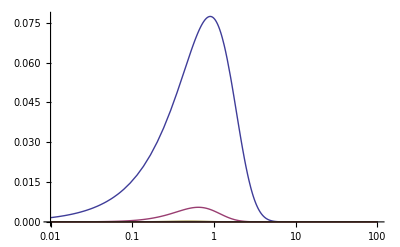

```mathematica
LogLinearPlot[Evaluate[Table[Tooltip[Subscript[P, m][m t]/Z[m t],m]/.{λ->1.0,r->0.08},{m,2,8}]],{t,0.01,100},PlotRange->All,AxesLabel->{t/m}]
```

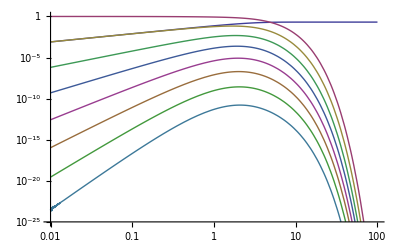

```mathematica
LogLogPlot[Evaluate[Table[Tooltip[Subscript[P, m][t],m]/.{λ->1.0,r->0.08},{m,0,8}]],{t,0.01,100},PlotRange->{10^-25, 1},AxesLabel->{t}]
```